# mPIMC

Copyright (C) 2017 Thomas Whitehead

This is mPIMC, a bosonic Path Integral Monte Carlo code written in Mathematica.  The aim of mPIMC is to provide an easy-to-understand, easy-to-modify, easy-to-generalise code base that is still efficient for simulations of larger systems.

mPIMC was designed with cold atomic gas simulations in mind; as such, it works with finite systems, allowing the explicit inclusion of external traps, harmonic or otherwise.

This is an explicitly parallel code; it will set up and use as many kernels as it can on the system you run it on.  This parallelisation is used simply to reduce statistical error bars in the results.

To use mPIMC, simply run each cell that you find when scrolling down this notebook.  This will run a simple Path Integral Monte Carlo simulation of two bosons in an harmonic trap.


To run your own simulation, modify the “Variables” block using the descriptions of the keywords found there, making sure you’ve loaded in mPIMC using the “Loading mPIMC” block.

Then set the external and inter-particle potentials in the “Potentials” block, and run the “Initialisation” block to generate the starting configurations of particles.

Finally, when you’re happy with the system set-up, run the “Running Calls” block, which will run a Path Integral Monte Carlo simulation using your given inputs.

If you find a bug (or, even better, fix a bug) in this code, please let me know via tmw38@tcm.phy.cam.ac.uk and I’ll put a fix in the main version.

## Loading mPIMC

```mathematica
<<mPIMC`
```

## Variables

```mathematica
(*The dimensionality of the system - 3 or 2 supported                                 Integer*)dimensionality=2;
(*ℏ/2m for particle mass m                                                               Real*)λ=0.5;
(*The time step of the simulation, also a measure of inverse temperature                 Real*)τ=0.05;
(*Number of beads/slices per particle; more lowers the temperature                    Integer*)slices=30;
(*Number of particles to include in the simulation                                    Integer*)numparticles=2;
(*Number of steps to run the simulation for                                           Integer*)numsteps=20000;
(*Number of steps to take between calculating observables                             Integer*)observablecalc=200;
(*Number of steps to take to equilibrate before starting calculating observables      Integer*)equilibrationsteps=5000;
(*Smoothing lengths to use on plots                                            Array of reals*)binsize={0.1,0.05,0.025,0.0125};
(*Maximum number of particles to try permuting at once                                Integer*)maxcyclelength=4;
(*Whether to calculate estimators for the energy                                      Boolean*)calculateEnergy=True;
(*Whether to calculate the thermodynamic estimator for the energy (not recommended)   Boolean*)energyTherm=False;
(*Whether to calculate the virial estimator for the energy (not recommended)          Boolean*)energyVirial=False;
(*Whether to calculate a better virial estimator for the energy (recommended)         Boolean*)energyFullVirial=True;
(*Whether to calculate the Heinze estimator for the energy (not recommended)          Boolean*)energyHeinze=True;
(*Whether to calculate the particle density                                           Boolean*)calculateParticleDensity=True;
(*Whether to calculate the density-density (pair) correlation function                Boolean*)calculatePairCorrelationFunction=True;
(*Whether to draw 3D plot of observables (slow)                                       Boolean*)allow3DCorrelationPlots=True;
(*How many samples to use for each direction in 3D plots                              Integer*)plotPoints3D=30;
(*Whether to compare results to those from a single particle in an harmonic trap      Boolean*)harmonictrap=True;
(*Whether to calculate and show the autocorrelation in the energy                     Boolean*)showAutocorrelation=True;
(*Whether to show plots of sample configurations of particles                         Boolean*)showPaths=True;
(*Whether to calculate the fraction of particles sitting on the same lattice site     Boolean*)calculateFracSameWell=False;
(*A frequency used for comparison harmonic traps, or in the external potential           Real*)ω=1.0;
(*Range over which to look for minima to start the particles in                          Real*)startingRange=0.375π;
(*Sample spacing for identifying minima to start the particles in                        Real*)startingDelta=0.05;
```

## Potentials

```mathematica
(*The external potential for particles to move in; acts equally on all particles. pos is position vector*)mPIMC`Private`extV[pos_]:=1/2 ω^2 pos.pos;
(*The gradient of the external potential                                                                *)mPIMC`Private`derivExtV[pos_]:=ω^2 pos;
(*The inter-particle potential, which acts equally between all pairs of particles                       *)mPIMC`Private`intpartV[pos1_,pos2_]:=0.;
(*The gradient of the inter-particle potential, differentiated with respect to the first argument, pos1 *)mPIMC`Private`derivIntpartV[pos1_,pos2_]:={0.,0.};
```

## Initialisation

Appears to be at least one starting position with more than one particle: check if this is desired behaviour.  If not, try increasing startingRange or decreasing startingDelta.

Temperature kT=0.666667

Thermal wavelength √(2  λτ)=0.223607

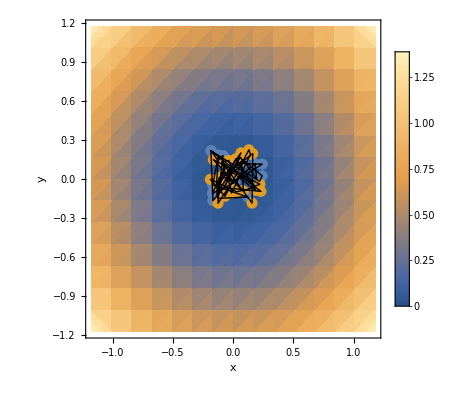

```mathematica
{originalpath,originaljoined}=initialisationloop[showPaths,λ,τ,slices,numparticles,numsteps,startingRange,startingDelta,dimensionality];
```

## Running calls

Temperature kT=0.666667

Run time of main loop: 34.7291s

Acceptance ratio bisection: 0.949967

Fractional time with permutations: 0.450583

Longest permutation cycle: 2 which is 1. of all particles

Ceperley virial weighted estimator of the energy per particle       : 1.24539+/-0.0326574

Heinze (unweighted) estimator of the energy per particle            : 1.39487+/-0.0487727

cf numerically exact total energy per non-interacting particle      : 1.57443

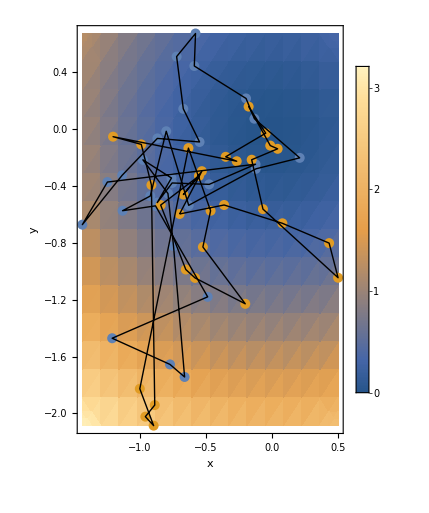
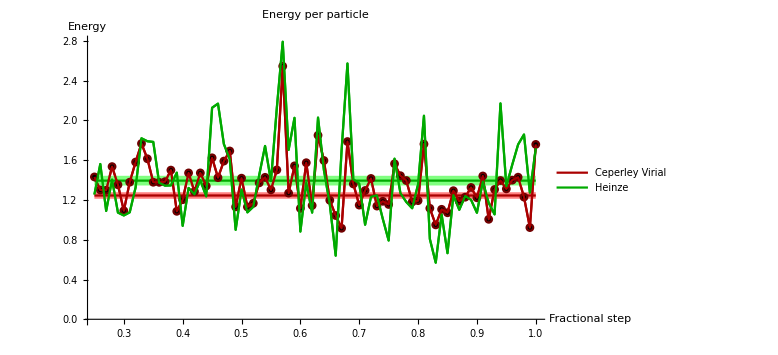
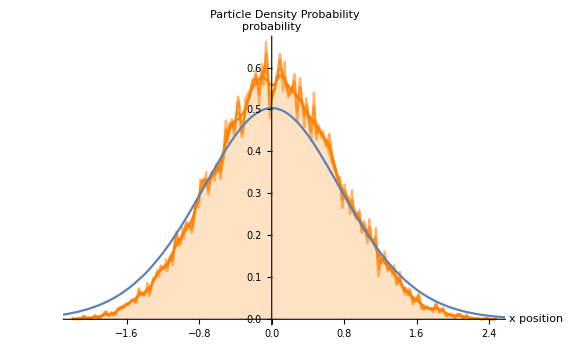
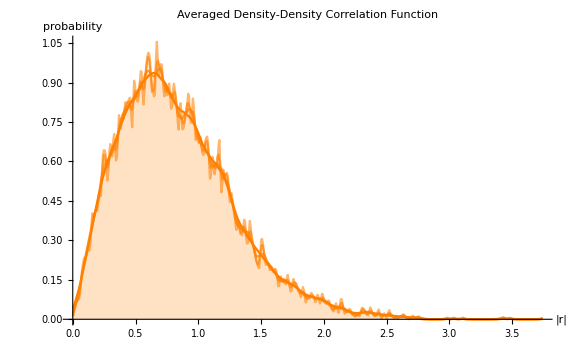
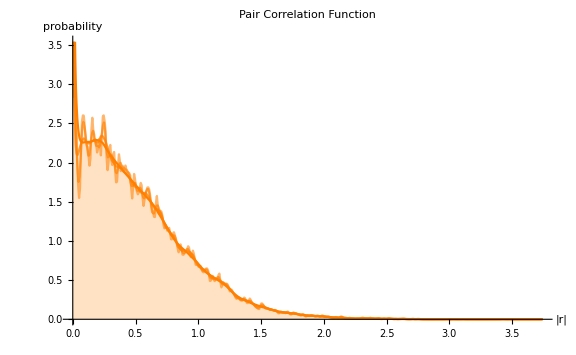
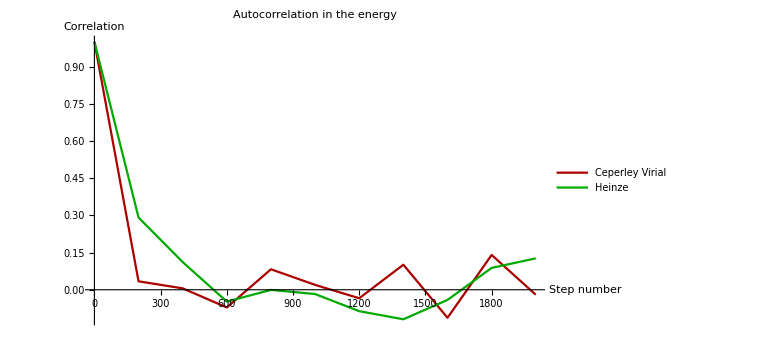
{-Graphics-,-Graphics-,-Graphics-,-Graphics3D-,-Graphics-,-Graphics-,-Graphics3D-,-Graphics3D-,-Graphics-}

```mathematica
Catch[ClearAll[energysaverarraytherm,invvartherm,energysaverarrayvirial,invvarvirial,energysaverarrayfullvirial,invvarfullvirial,energysaverarrayheinze,invvarheinze,particleDensitysaverarray,vectorPairCorrelationFunctionsaverarray,numsuccessesBisect,numpermuted,path,joined];
{energysaverarraytherm,invvartherm,energysaverarrayvirial,invvarvirial,energysaverarrayfullvirial,invvarfullvirial,energysaverarrayheinze,invvarheinze,particleDensitysaverarray,vectorPairCorrelationFunctionsaverarray,numsuccessesBisect,numpermuted,path,joined}=mainLoop[originalpath,originaljoined,λ,τ,calculateEnergy,calculateParticleDensity,calculatePairCorrelationFunction,maxcyclelength,dimensionality,numparticles,equilibrationsteps,observablecalc,numsteps,slices,energyTherm,energyVirial,energyFullVirial,energyHeinze,ω,harmonictrap,calculateFracSameWell,startingRange];
energyPrinter[calculateEnergy,energyTherm,energyVirial,energyFullVirial,energyHeinze,harmonictrap,energysaverarraytherm,invvartherm,energysaverarrayvirial,invvarvirial,energysaverarrayfullvirial,invvarfullvirial,energysaverarrayheinze,invvarheinze,τ,slices,ω,dimensionality];
plotMaker[showPaths,calculateEnergy,calculateParticleDensity,calculatePairCorrelationFunction,allow3DCorrelationPlots,showAutocorrelation,numparticles,path,joined,energyVirial,energyFullVirial,energyTherm,energyHeinze,energysaverarrayvirial,energysaverarrayfullvirial,energysaverarraytherm,energysaverarrayheinze,invvarvirial,invvarfullvirial,invvartherm,invvarheinze,equilibrationsteps,numsteps,harmonictrap,ω,τ,slices,particleDensitysaverarray,vectorPairCorrelationFunctionsaverarray,binsize,observablecalc,plotPoints3D,dimensionality]]
```